## Summation Index

```mathematica
Clear@LargestContiguousSum
LargestContiguousSum[nums_List]:=With[{sums=Array[Sum[nums[[k]],{k,##}]&,Length@nums {1,1}]},{Max@sums,nums[[Span@##]]}&@@@Position[sums,Max@sums]]//AbsoluteTiming
LargestContiguousSum@{1,2,3,4,5,-1,7,-4,-2}
LargestContiguousSum@{-4,1,2,3,4,5,-1,7,-2}
LargestContiguousSum@{-4,1,2,3,4,5,7,-1,-2}
LargestContiguousSum@{41,-45,88,59,59,-9,97,0,-1,1}
```

```mathematica
DiscretePlot[
AbsoluteTiming[LargestContiguousSum@RandomInteger[{-100,100},n]]⟦1⟧,
{n,1,501,10},
Joined->True,
Filling->False,
PlotStyle->Thickness[.006],
Frame->True,
FrameLabel->{"List Length","Time [s]"}
]
```

## Total of Ragged Spans

```mathematica
Clear@LargestContiguousSum2
LargestContiguousSum2[nums_List]:=Block[
{sums=Table[Total@nums⟦j;;k⟧,{j,#},{k,j,#}]&@Length@nums,maxsums},maxsums=Max@sums;
{maxsums,nums[[Span@##]]}&@@@Replace[Position[sums,maxsums],{a_,b_}:>{a,b+a-1},{-2}]
]
LargestContiguousSum2@{1,2,3,4,5,-1,7,-4,-2}
LargestContiguousSum2@{-4,1,2,3,4,5,-1,7,-2}
LargestContiguousSum2@{-4,1,2,3,4,5,7,-1,-2}
LargestContiguousSum2@{41,-45,88,59,59,-9,97,0,-1,1}
```

```mathematica
DiscretePlot[
AbsoluteTiming[LargestContiguousSum2@RandomInteger[{-100,100},n]]⟦1⟧,
{n,1,1001,10},
Joined->True,
Filling->False,
PlotStyle->Thickness[.006],
Frame->True,
FrameLabel->{"List Length","Time [s]"}
]
```

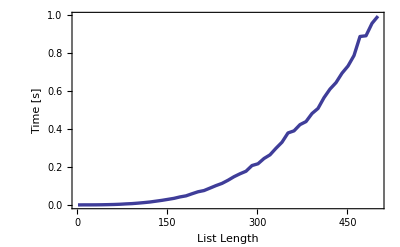
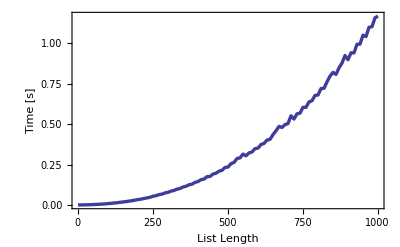
```mathematica
(*GraphicsRow[{Show[-Graphics-,PlotLabel->"Method 1"],Show[-Graphics-,PlotLabel->"Method 2"]},ImageSize->Large,Spacings->0]
SetDirectory@NotebookDirectory[];Export["method.png",%]*)
```